```mathematica
<<myFunctionsMathematica8.m
```

{Temporary}

```mathematica
strm=OpenRead["2000 better zeros copy 2"];
zrs=ReadList[strm];
zero[n_]:=zrs[[n]]
```

```mathematica
bestzero[n_]:=1/2+I*t[n]
```

## n \mapsto t[n] is defined as a table in myFunctionsPureCodeV8 copy.nb, whhich is loaded by myFunctionsMathematica8.m. The table was created in my2ndEditOdlyzkoAccrtZrs6dec15.nb. It is from a table on Odlyzko’s site.

```mathematica
zetaIterate[s_,iteratenumber_]:=Module[{kk,w},
w=s;
For[kk=0,kk<iteratenumber,kk++;w=Zeta[w];
If[Abs[w]>10^10,Break[]]];
Return[w]
];
Attributes[zetaIterate]=Listable
```

Listable

```mathematica
minimize[f_,center_,range_,grain_]:=
Module[{best,j,k,inc,seed,start},
start=SessionTime[];
inc=range/grain;
best={center,f[center]};
For[k=-range/2-inc,k<range/2,k=k+inc;
kminimize=k;
row={};
For[j=-range/2-inc,j<range/2,j=j+inc;
jminimize=j;
seed=center+j+k*I;


If[f[seed]<best[[2]],best={seed,f[seed]}];

]
];
Return[best]

]
```

```mathematica
zeroFinder5[f_,startcenter_,startrange_,rangedivider_,grain_,depth_]:=
Module[{g,j,m,mz,s,best,oldmz,newrange,newcenter},
best={Infinity,Infinity};
g[s_]:=Abs[f[s]];
newrange=startrange;
newcenter=startcenter;
For[m=0,m<depth,m++;
outm=m;
mz=minimize[g,newcenter,newrange,grain];
If[Not[Abs[mz[[2]]]<best[[2]]],Return[best]];
If[Abs[mz[[2]]]<best[[2]],
best=mz;
newrange=newrange/rangedivider;
newcenter=best[[1]]]];
Return[best]]
```

```mathematica
stream=OpenWrite["realfxpts26feb16no5"];
precision=500;
f[s_]:=zetaIterate[s,1]-s;
startrange=.002;
rangedivider=2;
grain=20;
depth=20;
For[n=18,n<100,n=n+2;
startcenter=-n;
fx=zeroFinder5[f,startcenter,startrange,rangedivider,grain,depth];
fxx=FindRoot[f[s],{s,fx[[1]]},WorkingPrecision->precision][[1,2]];
Write[stream,fxx]];
Close[stream]
```

realfxpts26feb16no5

```mathematica
stream=OpenRead["realfxpts26feb16no5"];
fxlist=ReadList[stream];
Close[stream];
Length[fxlist]
```

41

```mathematica
fxlist[[1]]
```

-20.13118630800828629570969261818903435246954374983095824829361336197298445037153047179548067402181278903368864978818252877598126801597699309131899845265831350000606234179346486628344281942168992233301869493872528861491794517990023610761043110184375395020951520898859194105542257615919088423030510749884702335706344501068226862000199916227170498140066484666521635807298061032820396516250657323488066821679092454038288517205167288129620561454671408721352521666783829381391197156669384513293609095228219+1.5545521416589045953277107041537525707269556316714469185957673575956904494147912899203657117558086622632407021201525283528876360998329997215806180213634491654672514756238570116605974888633627424187972962595296566780616959982373251978517171237007124651819044959621025560830139937357832940055112200192124934104913527382623260081183549283547520176961821968393073823763710464040323444131817663609832031988828798353364677743169717033944496779624975576850173642416126534442653699790717826999455058029349279×10^-505 ⅈ

```mathematica
fxlist[[8]]
```

-33.999999999683437233174912281325947102043539372533185107243450243754985913978980045452508326657173407993123812934937390426688552148328950638838043744450182917106993518488765286031837142371822140077112776084158697371235843899645917889174012178384353628820127982388570217777671931102117890747637081651199935506830840744882436645621085909017736011826167172953306409840287411360904248004303891930215315338205482804210351633648704950794641195239029807016477347425692848693841312777494049302718663493331609

```mathematica
For[n=0,n<8,n++;
data={};
arglog={};
fxx=fxlist[[n]];
zeros={bestzero[1]};
args={Arg[zeros[[1]]-fxx]};
For[k=1,k<200,k++;
startcenter=fxx;
x=zeros[[k-1]];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->498,WorkingPrecision->498][[1,2]];
zeros=Append[zeros,zr];

arg=Arg[zr-fxx];
args=Append[args,arg];
la=Log[Abs[zr-fxx]];
arglog=Append[arglog,{arg,la}];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point]];
Print["--------------------------------------------------"];
Print["fixed point ",n];
Print[ListPlot[data]];
Print[ListPlot[args]];
Print[ListPlot[arglog]]
];
```

--------------------------------------------------

## leaf5.7r1c1

fixed point 1

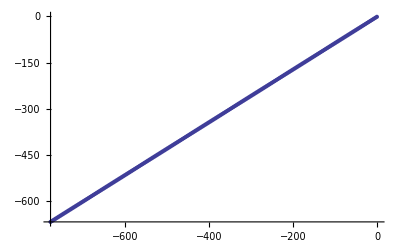

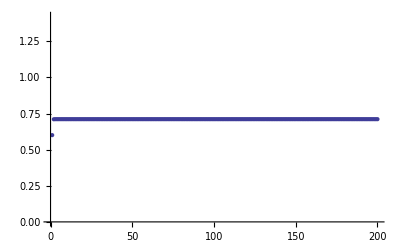

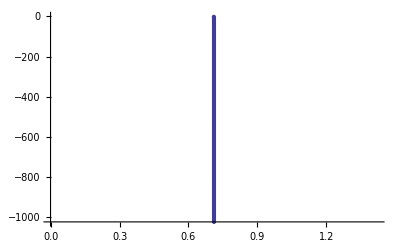

--------------------------------------------------

## leaf5.7r2c1

fixed point 2

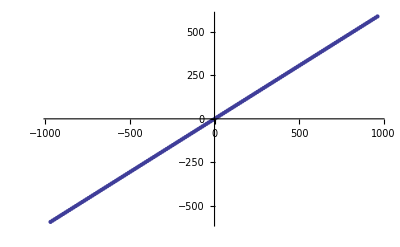

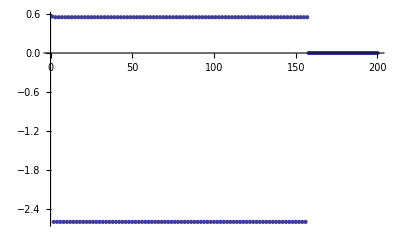

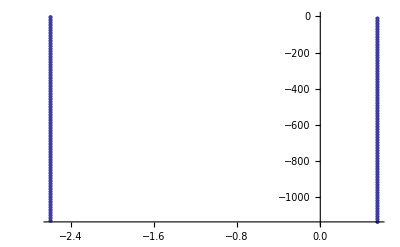

--------------------------------------------------

## leaf5.7r3c1

fixed point 3

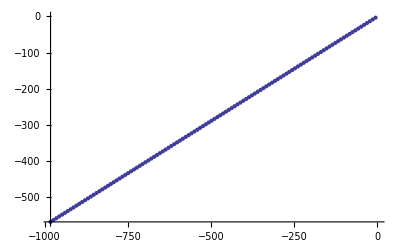

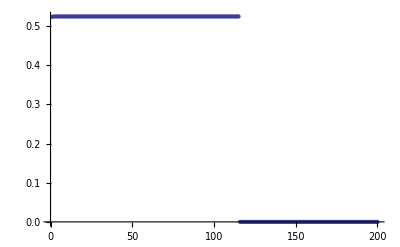

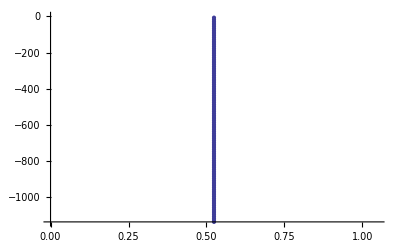

--------------------------------------------------

## leaf5.7r4c1

fixed point 4

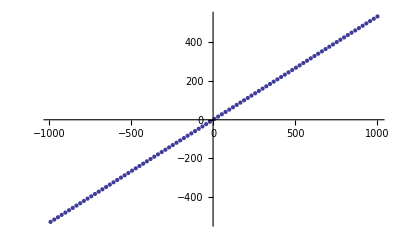

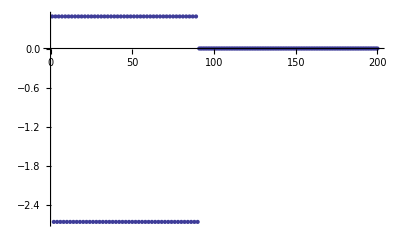

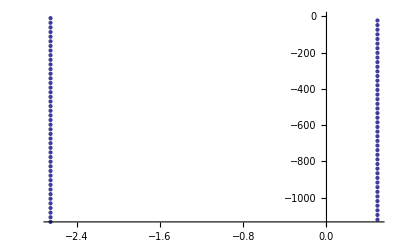

--------------------------------------------------

fixed point 5

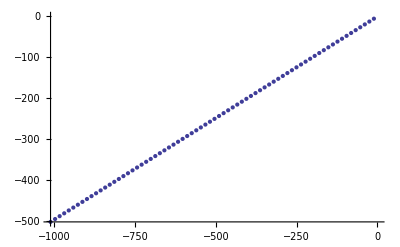

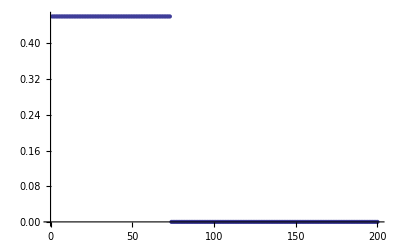

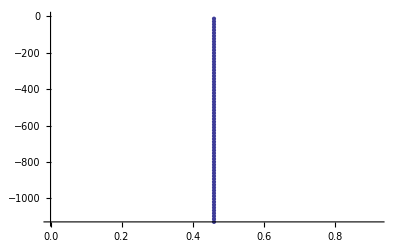

--------------------------------------------------

fixed point 6

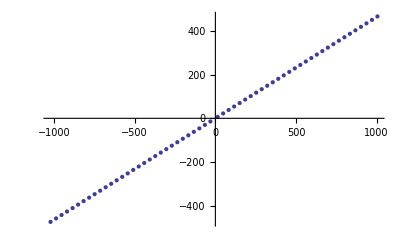

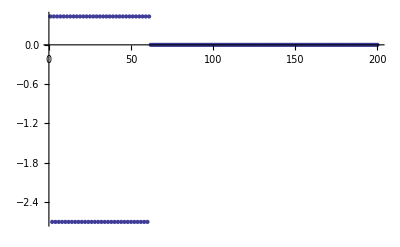

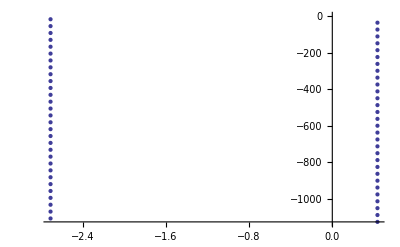

--------------------------------------------------

fixed point 7

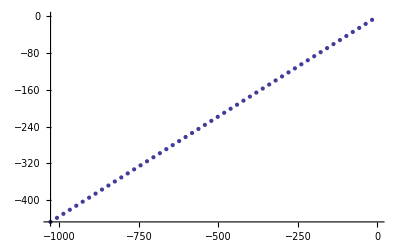

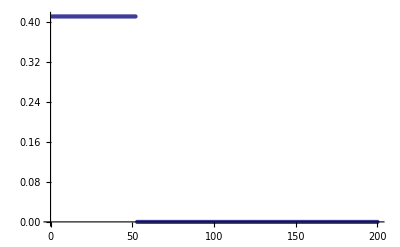

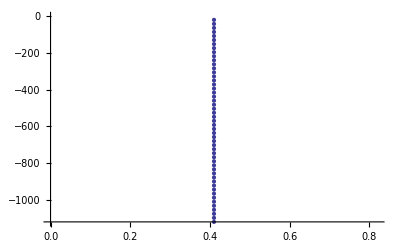

--------------------------------------------------

fixed point 8